This calculation is for a two plaquette system with periodic boundary conditions and mirroring between the upper and lower links on a matterless lattice. Using Soni and Trivedi’s definition of entanglement entropy, the entanglement entropy is calculated for an SU(3) gauge theory with truncation at the 3 and 3 bar representations.

Here, we define the necessary variables. The system is set up using qutrits. A link in the singlet representation is represented by (1,0,0); a link in the 3 representation is represented by (0,1,0) and a link in the 3 bar representation is represented by (0,0,1).

```mathematica
k1:={{1},{0},{0}}
k3:={{0},{1},{0}}
k3b:={{0},{0},{1}}
k111:=KroneckerProduct[KroneckerProduct[k1,k1],k1]
k13b1:=KroneckerProduct[KroneckerProduct[k1,k3b],k1]
k131:=KroneckerProduct[KroneckerProduct[k1,k3],k1]
k33b3:=KroneckerProduct[KroneckerProduct[k3,k3b],k3]
k3b33b:=KroneckerProduct[KroneckerProduct[k3b,k3],k3b]
k313:=KroneckerProduct[KroneckerProduct[k3b,k1],k3b]
k3b13b:=KroneckerProduct[KroneckerProduct[k3,k1],k3]
k333:=KroneckerProduct[KroneckerProduct[k3,k3],k3]
k3b3b3b:=KroneckerProduct[KroneckerProduct[k3b,k3b],k3b]
k311:=KroneckerProduct[KroneckerProduct[k3,k1],k1]
k3b11:=KroneckerProduct[KroneckerProduct[k3b,k1],k1]
k133:=KroneckerProduct[KroneckerProduct[k1,k3],k3]
k13b3b:=KroneckerProduct[KroneckerProduct[k1,k3b],k3b]
k33b3b:=KroneckerProduct[KroneckerProduct[k3,k3b],k3b]
k3b33:=KroneckerProduct[KroneckerProduct[k3b,k3],k3]
```

Now we construct the Hamiltonian. This was calculated by hand. The Hamiltonian for SU(3) gauge theory is given by the equation .  A term of 500I is added; this does not affect the eigenvectors but does ensure the eigenvalues are positive definite, which allows the eigenvectors to be ordered from largest eigenvalue to smallest eigenvalue.

```mathematica
Hb33[g_,a_]:=1/(2g^2a^2){{6,0,0,-1,-1,-1,-1,0,0},{0,6,0,-1,0,-1,0,-1,-1},{0,0,6,0,-1,0,-1,-1,-1},{-1,-1,0,6,-1,0,0,0,-1},{-1,0,-1,-1,6,0,0,-1,0},{-1,-1,0,0,0,6,-1,-1,0},{-1,0,-1,0,0,-1,6,0,-1},{0,-1,-1,0,-1,-1,0,6,0},{0,-1,-1,-1,0,0,-1,0,6}}
He33[g_]:=g^2/2{{0,0,0,0,0,0,0,0,0},{0,16/3,0,0,0,0,0,0,0},{0,0,16/3,0,0,0,0,0,0},{0,0,0,16/3,0,0,0,0,0},{0,0,0,0,16/3,0,0,0,0},{0,0,0,0,0,16/3,0,0,0},{0,0,0,0,0,0,16/3,0,0},{0,0,0,0,0,0,0,8,0},{0,0,0,0,0,0,0,0,8}}
H33[g_,a_]:=He33[g]+Hb33[g,a]+500IdentityMatrix[9]
```

We can now calculate the ground state of the Hamiltonian by looking at the lowest-energy eigenstates and construct our possible reduced density matrices.

```mathematica
GS33[g_,a_]:=Part[Eigenvectors[H33[g,a]],9]
a1[g_,a_]:=Part[GS33[g,a],1]k111
a2[g_,a_]:=Part[GS33[g,a],2]k13b1
a3[g_,a_]:=Part[GS33[g,a],3]k131
a4[g_,a_]:=Part[GS33[g,a],4]k33b3
a5[g_,a_]:=Part[GS33[g,a],5]k3b33b
a6[g_,a_]:=Part[GS33[g,a],6]k3b13b
a7[g_,a_]:=Part[GS33[g,a],7]k313
a8[g_,a_]:=Part[GS33[g,a],8]k333
a9[g_,a_]:=Part[GS33[g,a],9]k3b3b3b
b1[g_,a_]:=Part[GS33[g,a],1]k111
b2[g_,a_]:=Part[GS33[g,a],2]k311
b3[g_,a_]:=Part[GS33[g,a],3]k3b11
b4[g_,a_]:=Part[GS33[g,a],4]k133
b5[g_,a_]:=Part[GS33[g,a],5]k13b3b
b6[g_,a_]:=Part[GS33[g,a],6]k33b3b
b7[g_,a_]:=Part[GS33[g,a],7]k3b33
b8[g_,a_]:=Part[GS33[g,a],8]k333
b9[g_,a_]:=Part[GS33[g,a],9]k3b3b3b
RDM33A[g_,a_]:=
a1[g,a].Transpose[a1[g,a]]+a1[g,a].Transpose[a4[g,a]]+a1[g,a].Transpose[a5[g,a]]+
a2[g,a].Transpose[a2[g,a]]+a2[g,a].Transpose[a6[g,a]]+a2[g,a].Transpose[a8[g,a]]+
a3[g,a].Transpose[a3[g,a]]+a3[g,a].Transpose[a7[g,a]]+a3[g,a].Transpose[a9[g,a]]+
a4[g,a].Transpose[a1[g,a]]+a4[g,a].Transpose[a4[g,a]]+a4[g,a].Transpose[a5[g,a]]+
a5[g,a].Transpose[a1[g,a]]+a5[g,a].Transpose[a4[g,a]]+a5[g,a].Transpose[a5[g,a]]+
a6[g,a].Transpose[a2[g,a]]+a6[g,a].Transpose[a6[g,a]]+a6[g,a].Transpose[a8[g,a]]+
a7[g,a].Transpose[a3[g,a]]+a7[g,a].Transpose[a7[g,a]]+a7[g,a].Transpose[a9[g,a]]+
a8[g,a].Transpose[a2[g,a]]+a8[g,a].Transpose[a6[g,a]]+a8[g,a].Transpose[a8[g,a]]+
a9[g,a].Transpose[a3[g,a]]+a9[g,a].Transpose[a7[g,a]]+a9[g,a].Transpose[a9[g,a]]
RDM33B[g_,a_]:=
b1[g,a].Transpose[b1[g,a]]+b1[g,a].Transpose[b6[g,a]]+b1[g,a].Transpose[b7[g,a]]+
b2[g,a].Transpose[b2[g,a]]+b2[g,a].Transpose[b4[g,a]]+b2[g,a].Transpose[b9[g,a]]+
b3[g,a].Transpose[b3[g,a]]+b3[g,a].Transpose[b5[g,a]]+b3[g,a].Transpose[b8[g,a]]+
b4[g,a].Transpose[b2[g,a]]+b4[g,a].Transpose[b4[g,a]]+b4[g,a].Transpose[b9[g,a]]+
b5[g,a].Transpose[b3[g,a]]+b5[g,a].Transpose[b5[g,a]]+b5[g,a].Transpose[b8[g,a]]+
b6[g,a].Transpose[b1[g,a]]+b6[g,a].Transpose[b6[g,a]]+b6[g,a].Transpose[b7[g,a]]+
b7[g,a].Transpose[b1[g,a]]+b7[g,a].Transpose[b6[g,a]]+b7[g,a].Transpose[b7[g,a]]+
b8[g,a].Transpose[b3[g,a]]+b8[g,a].Transpose[b5[g,a]]+b8[g,a].Transpose[b8[g,a]]+
b9[g,a].Transpose[b2[g,a]]+b9[g,a].Transpose[b4[g,a]]+b9[g,a].Transpose[b9[g,a]]
```

From here, we are able to calculate the entanglement entropies () by simply using the eigenvalues of the reduced density matrices. We only use the first three eigenvalues, because the rest are zero or close enough to zero to vanish anyway.

```mathematica
S33A[g_,a_]:=-Part[Eigenvalues[RDM33A[g,a]],1]Log[Part[Eigenvalues[RDM33A[g,a]],1]]-Part[Eigenvalues[RDM33A[g,a]],2]Log[Part[Eigenvalues[RDM33A[g,a]],2]]-Part[Eigenvalues[RDM33A[g,a]],3]Log[Part[Eigenvalues[RDM33A[g,a]],3]]
S33B[g_,a_]:=-Part[Eigenvalues[RDM33B[g,a]],1]Log[Part[Eigenvalues[RDM33B[g,a]],1]]-Part[Eigenvalues[RDM33B[g,a]],2]Log[Part[Eigenvalues[RDM33B[g,a]],2]]-Part[Eigenvalues[RDM33B[g,a]],3]Log[Part[Eigenvalues[RDM33B[g,a]],3]]
```

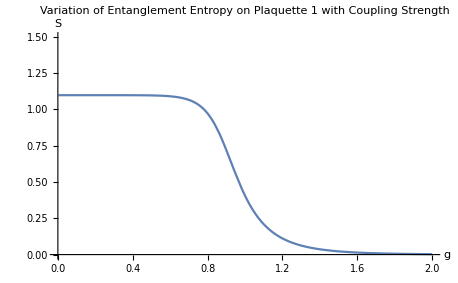

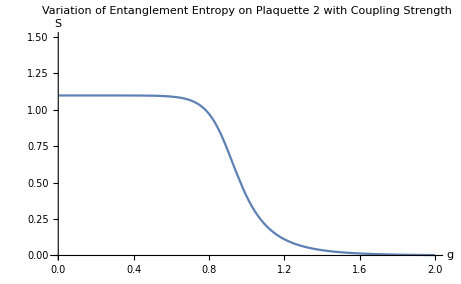

```mathematica
Plot[S33A[g,1],{g,Sqrt[0.00001],2},AxesLabel->{"g","S"},PlotLabel->"Variation of Entanglement Entropy on Plaquette 1 with Coupling Strength",PlotRange->{{0,2},{0,1.5}}]
Plot[S33B[g,1],{g,Sqrt[0.00001],2},AxesLabel->{"g","S"},PlotLabel->"Variation of Entanglement Entropy on Plaquette 2 with Coupling Strength",PlotRange->{{0,2},{0,1.5}}]
```

Examine what happens to the wavefunctions as we vary g:

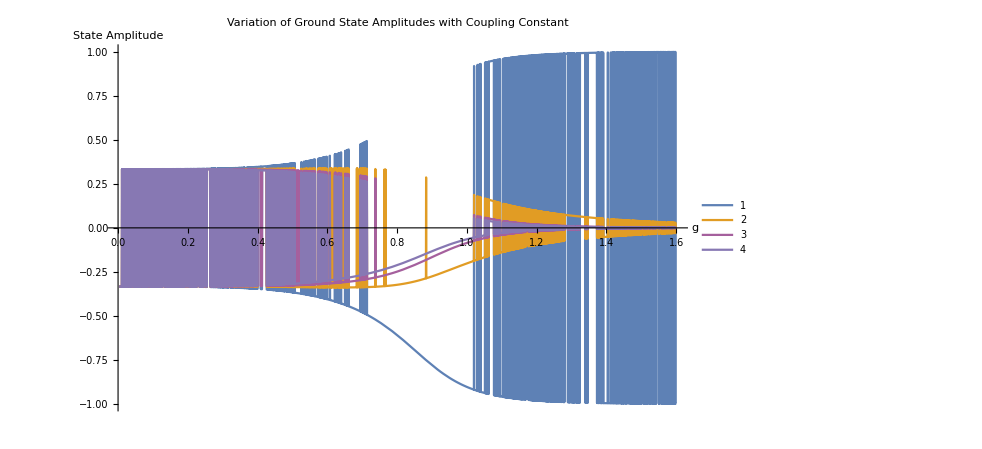

```mathematica
Plot[{Part[GS33[g,1],1],Part[GS33[g,1],5],Part[GS33[g,1],2],Part[GS33[g,1],9]},{g,Sqrt[0.00001],1.6},AxesLabel->{"g","State Amplitude"},PlotLabel->"Variation of Ground State Amplitudes with Coupling Constant",PlotLegends->LineLegend[Automatic],PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][9],ColorData[97][5],ColorData[97][1],ColorData[97][2],ColorData[97][9],ColorData[97][5]}]
```

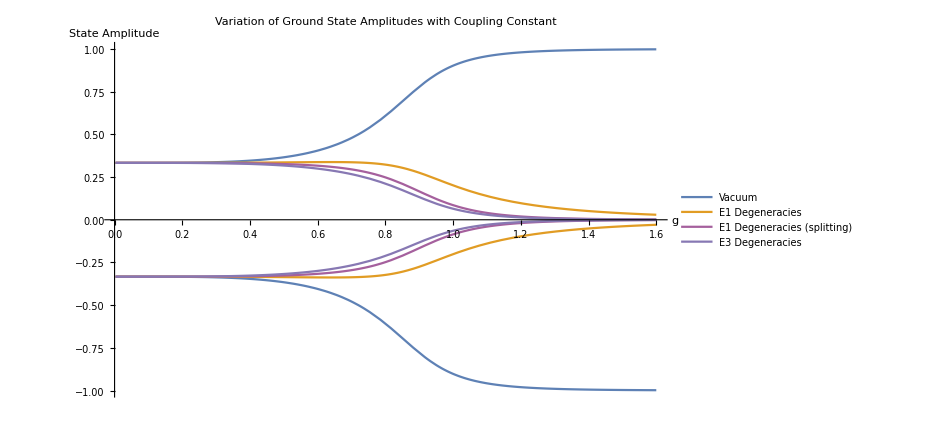

```mathematica
Plot[{Abs[Part[GS33[g,1],1]],Abs[Part[GS33[g,1],5]],Abs[Part[GS33[g,1],2]],Abs[Part[GS33[g,1],8]],-Abs[Part[GS33[g,1],1]],-Abs[Part[GS33[g,1],5]],-Abs[Part[GS33[g,1],2]],-Abs[Part[GS33[g,1],8]]},{g,Sqrt[0.00001],1.6},AxesLabel->{"g","State Amplitude"},PlotLabel->"Variation of Ground State Amplitudes with Coupling Constant",PlotLegends->LineLegend[{"Vacuum","E1 Degeneracies", "E1 Degeneracies (splitting)", "E3 Degeneracies"}],PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][9],ColorData[97][5],ColorData[97][1],ColorData[97][2],ColorData[97][9],ColorData[97][5]}]
```

```mathematica
Manipulate[GS33[g,1],{g,Sqrt[0.00001],2}]
```

```mathematica
Manipulate[MatrixForm[H33[g,1]],{g,Sqrt[0.0001],2}]
```

First states to freeze out are the 3333 and 3b3b3b3b states; the next two the vanish are the 313b1 and 3b131 states. Makes sense for them to vanish in pairs since they’re just different orientations of the same states. Also makes sense relative to energies I think; 3333 have the highest chromoelectric energies, followed by 313b1. Makes sense Hamiltonian wise, since with high coupling, the chromoelectric energies dominate and contributions from the magnetic field vanish, while at low coupling, the magnetic terms are stronger and the chromoelectric energies are weaker. So at high coupling, the only contributions to the ground state energy should be from the chromoelectric energy, so we want the states with the smallest possible chromoelectric energy. States vanish according to how much energy they contribute; there’s a splitting in the 2-7 states because 2-3 are coupled to 8 and 9, which have higher energies, so they have less “effective energy” than 4-7, since they require 8 and 9 to be in the system in order to decrease their energy as much as 4-7 do (which also have coupling to the lowest energy states). 

Is the area around  a second-order phase transition? Order parameter would be?

What does it mean in context of entropy? Concept of entanglement entropy is to measure how “mixed” a state we’re in. So the ground state is in a very mixed state with high entanglement entropy, but when we end up with only a single state, we’re in a very pure state. So, I’ve split the system into two plaquettes, and I trace out the second one. The resulting entropy is a measure of the degree of entanglement between the two plaquettes. If the ground state consists of a combination of multiple different states, then there’s entanglement between the two plaquettes, which makes sense since they’re not cleanly separable. Each individual state itself is separable, and if there’s only one, then I’m unentangled. So this matches the way I would expect. Below a certain coupling strength (~), the mixture of states in the ground state doesn’t change much and is pretty stable, with every state roughly equally represented.

Just to confirm that the eigenvalues vanish aside from the first three (should probably figure out why). :

```mathematica
Manipulate[Eigenvalues[RDM33A[g,1]],{g,Sqrt[0.00001],2}]
```

```mathematica
Manipulate[Eigenvalues[RDM33B[g,1]],{g,Sqrt[0.00001],2}]
```

```mathematica
Manipulate[{Transpose[{{1},{0},{0},{0},{0},{0},{0},{0},{0}}].(H33[g,1]-500IdentityMatrix[9]).{{1},{0},{0},{0},{0},{0},{0},{0},{0}},Transpose[{{0},{1},{0},{0},{0},{0},{0},{0},{0}}].(H33[g,1]-500IdentityMatrix[9]).{{0},{1},{0},{0},{0},{0},{0},{0},{0}},Transpose[{{0},{0},{0},{1},{0},{0},{0},{0},{0}}].(H33[g,1]-500IdentityMatrix[9]).{{0},{0},{0},{1},{0},{0},{0},{0},{0}},Transpose[{{0},{0},{0},{0},{0},{0},{0},{1},{0}}].(H33[g,1]-500IdentityMatrix[9]).{{0},{0},{0},{0},{0},{0},{0},{1},{0}}},{g,Sqrt[0.00001],2}]
```

All the states have the same expectation value of energy at weak coupling, and separate into different energies at stronger coupling. Top is |1111>, middle are |3131> |1333> and |3313>, bottom are |3333>.

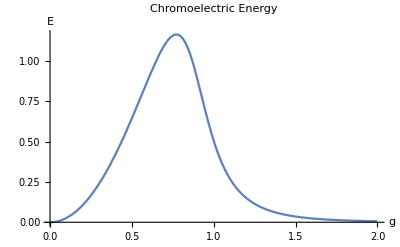

```mathematica
Manipulate[Transpose[GS33[g,1]].Hb33[g,1].GS33[g,1],{g,Sqrt[0.00001],2}]
Manipulate[Transpose[GS33[g,1]].He33[g].GS33[g,1],{g,Sqrt[0.00001],2}]
Plot[Transpose[GS33[g,1]].He33[g].GS33[g,1],{g,Sqrt[0.00001],2},AxesLabel->{"g","E"},PlotLabel->"Chromoelectric Energy"]
```

And as expected, the magnetic contribution to energy falls off dramatically for the ground state as the coupling strength increases, while the electric contribution to energy actually follows an interesting curve corresponding to the freezing out of higher-flux states.

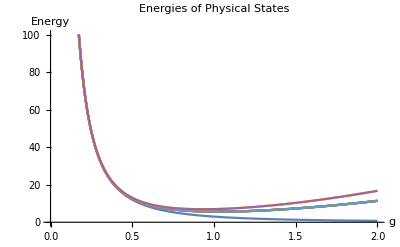

```mathematica
Plot[{Part[Part[H33[g,1]-500IdentityMatrix[9],1],1],Part[Part[H33[g,1]-500IdentityMatrix[9],2],2],Part[Part[H33[g,1]-500IdentityMatrix[9],3],3],Part[Part[H33[g,1]-500IdentityMatrix[9],4],4],Part[Part[H33[g,1]-500IdentityMatrix[9],5],5],Part[Part[H33[g,1]-500IdentityMatrix[9],6],6],Part[Part[H33[g,1]-500IdentityMatrix[9],7],7],Part[Part[H33[g,1]-500IdentityMatrix[9],8],8],Part[Part[H33[g,1]-500IdentityMatrix[9],9],9]},{g,Sqrt[0.00001],2},AxesLabel->{"g","Energy"},PlotLabel->"Energies of Physical States",PlotRange->{{0,2},{0,100}}]
```